# Mass transfer stability for finite temperature white dwarfs

Nelemans+2001 https://arxiv.org/pdf/astro-ph/0101123

## Physical constants

```mathematica
Msol = 2 10^33;
Rsol = 6.955 10^10;
G=6.67 10^-8;
c=3 10^10;
```

## Reproduction of Nelemans+2001 Fig 1

### Some definitions

Eggleton' s zero - temperature mass–radius relation, quoted by Verbunt & Rappaport (1988), or Eq. 24:

```mathematica
Rcold[m1_]:=0.0114 ((m1/1.44)^(-2/3)-(m1/1.44)^(2/3))^(1/2)(1+3.5(m1/(5.7 10^-4))^(-2/3)+((5.7 10^-4)/m1))^(-2/3);
```

The derivative of the Roche radius in the small q approximation for Paczynski (1971) is just 1/3.

```mathematica
ζRL = 1/3;
```

The full derivative of the Roche radius in approximation of Eggleton (1983), which we will use, is given by

```mathematica
ζRLlist[m1_,m22_]=3/2 3^(1/3) m22^(2/3) (m1+m22)^(1/3) (-(2 m22^(1/3))/(9 3^(1/3) (m1+m22)^(4/3))+2/(9 3^(1/3) m22^(2/3) (m1+m22)^(1/3)));
```

From polytropic mass radius relation, Soberman 1997 etc. the primary radius changes with mass loss according to:

```mathematica
ζ2cold = -1/3;
```

### Curve 1: “dynamical stability boundary” - when radius expands faster than Roche radius upon mass loss (change in orbital angular momentum)

```mathematica
m1arr = Table[m1,{m1,0.0001,1.4,0.01}]//Flatten;
```

```mathematica
m1list=m1arr;
```

Solving Equation 20. for dynamical stability criteria, we get the primary mass m_2 for any m_1 between 0 and 1.4M_⊙

```mathematica
m2up=m22/.Table[FindRoot[(1+ ((ζ2cold-ζRLlist[m1,m22])/2) )m1 ==m22,{m22,1/5 m1}],{m1,0.0001,1.4,0.01}];
```

```mathematica
lineb= ListPlot[Transpose[{m1list,m2up}],Joined-> True,PlotStyle->{Black,Thickness[0.005]},AspectRatio-> 2/3,Frame->True,PlotRange-> {{0.1,1.4},{0,0.5}},LabelStyle->{(FontFamily->"Times"), Black},FrameLabel-> {Style["m_1 (M_⊙)",16],Style["m_2 (M_⊙)",16]},BaseStyle->{FontSize->16}];
lText=Graphics[Text["unstable merger",{0.36,0.45}]];
l1 = Transpose[{m1arr,m2up}];
l5= Transpose[{m1arr, 0 m2up +100}];
fill1 = ListPlot[{l5,l1},Mesh->All,PlotMarkers->None,Joined->True,Filling->{1->{2}},FillingStyle->{Blend[{Cyan,Cyan,Black}],Opacity[.3]},PlotStyle-> {{Blend[{Cyan,Cyan,Black}],Opacity[0.5]}},AspectRatio-> 2/3,Frame->True,PlotRange-> {{0.1,1.4},{0,0.5}},LabelStyle->{(FontFamily->"Times"), Black},FrameLabel-> {Style["m_1 (M_⊙)",16],Style["m_2 (M_⊙)",16]},BaseStyle->{FontSize->16}];
```

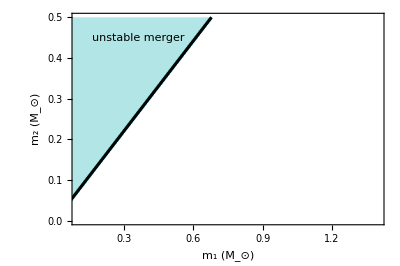

```mathematica
Show[lineb,fill1,lineb,lText]
```

### Curve 2: instability from super- Eddington direct impact accretion onto the accretor (assuming that mass transfer is conservative)

Here, the accretion rate driven by orbital angular momentum loss from GW emission is compared with the Eddington accretion rate of the donor m_1. This is because “heating of the transferred material, may cause it to expand and form a common envelope in which the two white dwarfs most likely merge (Han & Webbink 1999).”

... “Therefore, we impose the additional restriction to have the initial mass transfer rate lower than the Eddington accretion limit for the companion (∼ 10^-5 M_⊙ yr^-1).”

dJ/dt from GR, Eq . 1  (Landau & Lifshitz 1971). Replacing semi major axis a with  R/0.46 .. m_1 m_2 comes from Nelemans+2001 Equation 2. This R/0.46 part is compatible with what you would get using RRL = Rcold for a given mass ratio q = m_2/m_1, with m_2 being the less massive donor.

Note this is in cgs units - so input should be in g, cm.

```mathematica
JJ[m1_,m22_,R_]=-32/5 G^3/c^5(m1 m22 (m1 + m22))/((R/0.46((m1 +m22)/m22)^(1/3))^4);
```

For the Eddington mass accretion limit , there are hints in Hann and Webbink 1999 Eq. 18. And also details in 4.1 of Nelemans, and also Eq 34 in Marsh+2004. At least in Tutukov & Yungelson 1979, it is ~ 10^-5. 
Here we take a function that depends linearly on m_1 and amounts to ∼ 10^-5 M_⊙ yr^-1. (without some m_1 dependence, the function droops down)

The constant is chosen to reproduce Nelemans Fig 1. (but should be modified later with correct dependence etc.)

```mathematica
Medd22[m1_]:= 5 4.4 10^-6(m1)^2/(π 10^7)Msol
```

Now we compare this with rate of mass transfer for a semidetached binary, where the mass transfer is driven by gravitational waves (Paczynski 1967). This is dM/dt in Eq. 3 in Nelemans+2001. 

This is a product of dJ/dt and the inverse of the dynamical stability criteria (Equation 4) which includes how the donor radius, Roche radius, and mass ratio change upon mass transfer. This is:

```mathematica
Mdotacc[m1_,m22_]:= JJ[m1,m22,Rcold[m22/Msol]Rsol]m22 (1+ζ2cold/2-ζRLlist[m1,m22]/2- m22/m1)^-1
```

Note that this assumes that no angular momentum is lost in the system.

We equate this rate with the Eddington accretion rate

```mathematica
bounda=m22/.Table[FindRoot[Mdotacc[Msol m1,Msol m22]==-Medd22[m1],{m22,1/5 m1}],{m1,0.0001,1.4,0.01}]//Flatten;
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
linea=ListPlot[Transpose[{m1arr,bounda}],Joined-> True,PlotStyle->{Blend[{Magenta,Red}],Thickness[0.005]},Frame->True,PlotRange-> {{0.1,1.4},{0,0.5}},LabelStyle->{(FontFamily->"Times"), Black},FrameLabel-> {Style["m_1 (M_⊙)",16],Style["m_2 (M_⊙)",16]},BaseStyle->{FontSize->16}];
l2=Transpose[{m1arr,bounda}];
fill2 = ListPlot[{l1,l2},Mesh->All,PlotMarkers->None,Joined->True,Filling->{1->{2}},FillingStyle->{Magenta,Opacity[0.3]},PlotStyle-> {{Magenta,Opacity[0.3]}}];
cText=Graphics[Text["super-Eddington merger",{0.95,0.38}]];
```

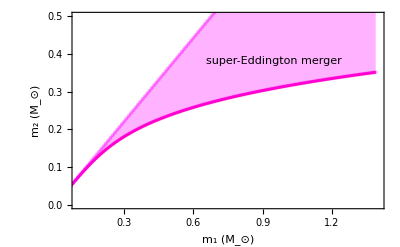

```mathematica
Show[linea,fill2,cText]
```

### Curve 3: boundary for direct impact accretion with completely inefficient spin coupling, i.e. where all AM in accretion stream is lost / AM sink)

Here, the extreme where all AM associated with the accretion stream is lost. In the usual stability criteria (Eq 4.) which is then used in Eq.3, an additional sink appears leading to Eq. 7.

R_h/a = r_h is the radius of the ring orbiting the accreting star. For an expression for r_h , we take  Verbunt & Rappaport (1988)’s Equation 13. This comes from a fit to Lubow and Shu (1975) for mass ratios of order unity,  but Hut and Paczynski (1984) did this for more extreme mass ratios. 
(See discussion about Eq. 7 . for it’s origin re: angular momentum loss.)

r_h given by Verbunt & Rappaport (1988):

```mathematica
rh[m1_,m22_]= 0.0883+0.04858( Log10[m1/m22])+0.11489 (Log10[m1/m22])^2-0.020475 (Log10[m1/m22])^3;
```

Including r_h leads to Equation 7 from Nelemans + 2001. This is used instead of Eq 4, into dM/dt (Eq. 3 in Nelemans+2001)

```mathematica
Mdotacc2[m1_,m22_]:= JJ[m1,m22,Rcold[m22/Msol]Rsol]m22 (1+ζ2cold/2-ζRLlist[m1,m22]/2-((1+m22/m1)rh[m22,m1])^(1/2)-m22/m1)^-1
```

Now equating this mass accretion rate dM/dt (which accounts for an accretion disc) with Eddington accretion

```mathematica
boundc=m22/.Table[FindRoot[Mdotacc2[Msol m1,Msol m22]==-Medd22[m1 ],{m22,1/5 m1}],{m1,0.0001,1.4,0.01}]//Flatten;
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
line3=ListPlot[Transpose[{m1arr,boundc}],Joined-> True,PlotStyle->{Blend[{Magenta,Red}],Dashed,Thickness[0.005]},AspectRatio-> 2/3,Frame->True,PlotRange-> {{0.1,1.4},{0,0.5}},LabelStyle->{(FontFamily->"Times"), Black},FrameLabel-> {Style["m_1 (M_⊙)",16],Style["m_2 (M_⊙)",16]},BaseStyle->{FontSize->16}];
l3 = Transpose[{m1arr,boundc}];
fill3 = ListPlot[{l2,l3},Mesh->All,PlotMarkers->None,Joined->True,Filling->{1->{2}},FillingStyle->{Blend[{Yellow,Yellow,Orange}],Opacity[.3]},PlotStyle-> {{Blend[{Yellow,Yellow,Orange}],Opacity[0.5]}}];
rText=Graphics[Text["direct impact",{0.69,0.2}]];
```

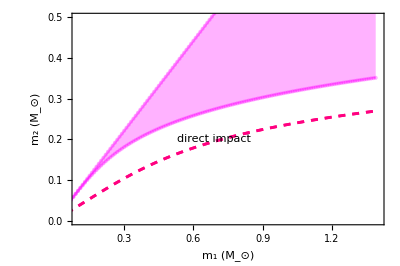

```mathematica
Show[line3,fill2,line3,rText]
```

This is the dashed boundary in Nelemans + 2001 Fig 1.

### The boundary between direct impact and Eddington mass transfer for a disc .

For the final line in Nelemans + 2001 Fig 1., around Eq. 6 they explain “The value of q at which the radius of the accretor equals rmin is presented as a dotted line in Fig. 1; above this line the accretion stream hits the white dwarfs’ surface directly and no accretion disk is formed”.
However, comparing this fit for r_min/a to Lubow & Shu (1975)’s ω_min, I can’t reproduce the Table values (using both natural Log, or Log 10)..
Instead, we use Marsh+2004 (equation 31, A17) but replacing r_h with r_1=R_1/a for the limit in the case of disc-fed accretion. Note that this goes into the mass transfer rate equation, Eq. 4.

The donor fills its Roche lobe, with R_2/a = R_RL/a given by:

```mathematica
RRLval[mp_,ms_]=(0.49(mp/ms)^(2/3))/(0.6 (mp/ms)^(2/3)+Log[1+(mp/ms)^(1/3)]);
```

```mathematica
RaNelemans[m1_,m22_] = 0.46((m1+m22)/m22)^(-1/3)
```

0.46/((m1+m22)/m22)^(1/3)

Since R_2is given by a mass radius relation, the semi major axis can be solved for, as a function of donor mass m_1.

```mathematica
aRL[m1_,m22_]=((Rcold[m22]Rsol)/RRLval[m22,m1]);
```

```mathematica
Mdotacc3[m1_,m22_]:= JJ[m1,m22,Rcold[m22/Msol]Rsol]m22 (1+ζ2cold/2-ζRL/2-((1+m22/m1)Rcold[m1/Msol]/(Rcold[m22/Msol] RRLval[m22/Msol,m1/Msol]^-1))^(1/2)-m22/m1)^-1
```

```mathematica
boundg=m22/.Table[FindRoot[Mdotacc3[Msol m1,Msol m22]==-Medd22[m1],{m22,1/5 m1}],{m1,0.0001,1.4,0.01}]//Flatten;
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::frmp: Machine precision is insufficient to achieve the accuracy {1.05367×10^-8,1.05367×10^-8}.

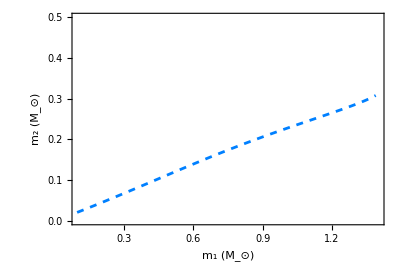

```mathematica
lineff=ListPlot[Transpose[{m1arr,boundg}],Joined-> True,PlotStyle->{Blend[{Cyan,Blue}],Dashed,Thickness[0.005]},AspectRatio-> 2/3,Frame->True,PlotRange-> {{0.1,1.4},{0,0.5}},LabelStyle->(FontFamily->"Times"),FrameLabel-> {Style["m_1 (M_⊙)",16],Style["m_2 (M_⊙)",16]},BaseStyle->{FontSize->16}]
```

alternatively, we can try according to what is written in Nelemans + 2001 anyway . Using Equation 6 in Nelemans + 2001 (log10 or log e ?)

```mathematica
rmin[q_]:=0.04948−0.03815 Log[q]+0.04752 (Log[q])^2−0.006973 (Log[q])^3
```

We want when r_min/a = R_accretor/a.

```mathematica
boundff2=m22/.Table[FindRoot[rmin[ m22/m1] ==Rcold[m1/Msol]/(Rcold[m22/Msol] RRLval[m22/Msol,m1/Msol]^-1),{m22, 1/5m1}],{m1,0.0001,1.4,0.01}];
```

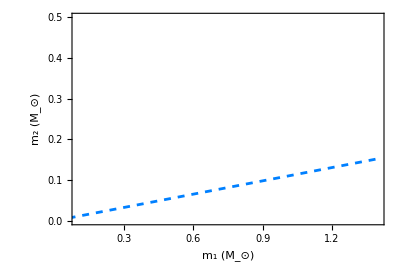

```mathematica
lineff=ListPlot[Transpose[{m1arr,boundff2}],Joined-> True,PlotStyle->{Blend[{Cyan,Blue}],Dashed,Thickness[0.005]},AspectRatio-> 2/3,Frame->True,PlotRange-> {{0.1,1.4},{0,0.5}},LabelStyle->(FontFamily->"Times"),FrameLabel-> {Style["m_1 (M_⊙)",16],Style["m_2 (M_⊙)",16]},BaseStyle->{FontSize->16}]
```

```mathematica
dText=Graphics[Text["accretion disc",{1,0.05}]];
l6= Transpose[{m1arr, 0 m2up }];
fill4 = ListPlot[{l3,l6},Mesh->All,PlotMarkers->None,Joined->True,Filling->{1->{2}},FillingStyle->{Blend[{Cyan,Cyan,Blue}],Opacity[.3]},PlotStyle-> {{Blend[{Cyan,Cyan,Blue}],Opacity[0.5]}}];
```

## Reproduction of Fig 1

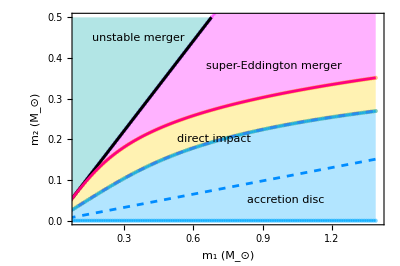

```mathematica
Show[lineb,fill1,fill2,fill3,lineb,linea,line3,lineff,fill4,lText,rText,dText,cText]
```